(0.
0.6
1.2
1.8
2.4
3.
3.6
4.2
4.8
5.4
6.) (0.0965324
0.11557
0.132937
0.146919
0.156003
0.159155
0.156003
0.146919
0.132937
0.11557
0.0965324)

0.0960864+0.033528 x-0.00187675 x^3+0.000157767 x^4

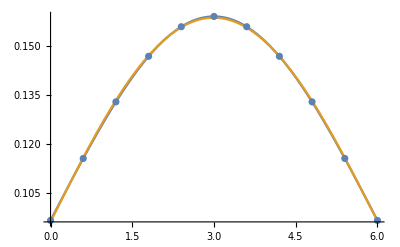

```mathematica
a=0;b=6;n=10;
h=(b-a)/n;
XDT={}; YDT={};
For[i=0,i≤n,i++, xdata[i]=N[a+i*h];ydata[i]=N[1/(2π)*Exp[-1/18(xdata[i])^2+1/3(xdata[i])-1/2]]; XDT=Append[XDT, xdata[i]];YDT=Append[YDT, ydata[i]];];
MatrixForm[XDT]MatrixForm[YDT]
Array[xdata,{n+1,0}];Array[ydata,{n+1,0}];
Clear[x]
data=Table[{N[xdata[i]], N[ydata[i]]},{i,0,n}];
Clear[a,b,c ,d]; rules= FindFit[data,a+b*x+c*x^3+d*x^4, {a,b,c,d},x];y=a+b*x+c*x^3+d*x^4/.rules
gr1:=Plot[{N[1/(2π)*Exp[-1/18 x^2+1/3 x-1/2]],y},{x,0,6}];
gr2:= ListPlot[Table[{N[xdata[i]],N[ydata[i]]},{i,0,n}]];
Show[{gr1,gr2}]
```

(0.
0.6
1.2
1.8
2.4
3.
3.6
4.2
4.8
5.4
6.) (0.0965324
0.11557
0.132937
0.146919
0.156003
0.159155
0.156003
0.146919
0.132937
0.11557
0.0965324)

0.0964093+0.0326897 x-0.00156294 x^3+0.0000575172 x^4+8.63079×10^-6 x^5

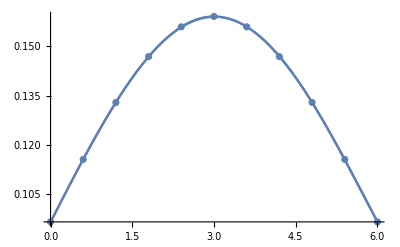

```mathematica
a=0;b=6;n=10;
h=(b-a)/n;
XDT={}; YDT={};
For[i=0,i≤n,i++, xdata[i]=N[a+i*h];ydata[i]=N[1/(2π)*Exp[-1/18(xdata[i])^2+1/3(xdata[i])-1/2]]; XDT=Append[XDT, xdata[i]];YDT=Append[YDT, ydata[i]];];
MatrixForm[XDT]MatrixForm[YDT]
Array[xdata,{n+1,0}];Array[ydata,{n+1,0}];
Clear[x]
data=Table[{N[xdata[i]], N[ydata[i]]},{i,0,n}];
Clear[a,b,c ,d,e]; rules= FindFit[data,a+b*x+c*x^3+d*x^4+e*x^5, {a,b,c,d,e},x];y=a+b*x+c*x^3+d*x^4+e*x^5/.rules
gr1:=Plot[N[1/(2π)*Exp[-1/18 x^2+1/3 x-1/2]],{x,0,6}];
gr2:= ListPlot[Table[{N[xdata[i]],N[ydata[i]]},{i,0,n}]];
gr3:=Plot[y,{x,0,6}];
Show[{gr1,gr2,gr3}]
```